# Berkson’s Paradox

Remove one quadrant.
The quadrant where both variables are negative.
Do this for uncorrelated variables.
This gives a fake negative correlation.

```mathematica
X = RandomVariate[NormalDistribution[],10^4];
Y = RandomVariate[NormalDistribution[],10^4];
Z=Transpose[{X,Y}];
Correlation[Z][[2]][[1]]
```

-0.00311412

```mathematica
Z2 = Select[Z, Sign[#[[1]]] + Sign[#[[2]]] > -2&];
Correlation[Z2][[2]][[1]]
```

-0.311458

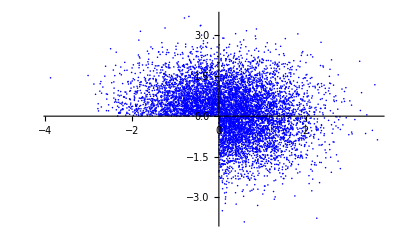

```mathematica
ListPlot[Z2,PlotStyle->Blue]
```

# With Bernoulli Distribution

Remove one quadrant.
The quadrant where both variables are negative.
Do this for uncorrelated variables.
This gives a fake negative correlation.

```mathematica
X = 2RandomVariate[BernoulliDistribution[1/2],10^4]-1;
Y = 2RandomVariate[BernoulliDistribution[1/2],10^4]-1;
Z=Transpose[{X,Y}];
Correlation[Z]//N
```

{{1.,-0.00838715},{-0.00838715,1.}}

```mathematica
Z2 = Select[Z, Sign[#[[1]]] + Sign[#[[2]]] > -2&];
Correlation[Z2] // N
```

{{1.,-0.498562},{-0.498562,1.}}